# Report Project 3

Course code: IX1500
Date: 2018-10-24

Rikard Jakobsson, rikjak@kth.se

Task 1: Dijkstra

## Summary

### Task

a) Explain how Dijkstra’s algorithm works. Use Mathematica graph-methods to illustrate your explanation with an animation.

### Result

Dijskstra’s algorithm finds the shortest path between two vertices in a graph by using a version of a breath first search. You start by marking the distance to all nodes directly reachable from the start node in a list, and setting the rest to infinity. You then add the reachable ones to a priority queue. For each element in the priority queue you check its adjacent nodes. If the distance to one of these is bigger than the current distance plus the distance there from the current node you update it and add the current node as the ‘parent’ to the node looked at. When this is done you can recursively get the shortest path to a node from the start node.

## Code

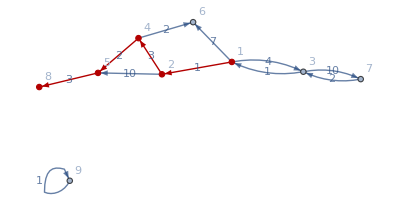

Part::partd: Part specification getFromQueue⟦1⟧ is longer than depth of object.

Part::pkspec1: The expression getFromQueue⟦1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

```mathematica
g = Graph[{1->2,1->3,1->6,2->4,2->5,3->7,3->1,4->5,4->6,5->8,7->3,9->9},EdgeWeight->{1,4,7,3,10,10,1,2,2,3,2,1},VertexLabels->Automatic,EdgeLabels->"EdgeWeight"];

FindShortestPath[g2,"a","h"];
HighlightGraph[g,PathGraph[FindShortestPath[g,1,8,Method->"Dijkstra"],DirectedEdges->True]]
distance = {};
parent = {};
dijkstra[graph_,from_,to_]:= (parent = ConstantArray[0,Length[VertexList[graph]]];
queue = {};
visited={};
distance =ConstantArray[Infinity,Length[VertexList[graph]]];
adjacent =Normal[WeightedAdjacencyMatrix[graph]];
parent[[from]] =from;
distance[[from]] = 0;
addToQueue[from];
While[queue≠{},(
element = getFromQueue[[1]];
fillDistance[element,element];
);
];
(*fillDistance[from,from];*)

addToQueue[node_]:=(AppendTo[queue,{node,distance[[node]]}];
Sort[queue,#1[[2]]<#2[[2]]&];
);
getFromQueue[]:=(a  = queue[[1]];
Delete[queue,1];
Return[a]
);
fillDistance[input_,row_]:=(For[i = 1,i<Length[adjacent[[row]]],i++,
If[adjacent[[row]][[i]]≠0,
(If[distance [[i]]>(adjacent[[row]][[i]]+distance[[input]]),
(distance [[i]]=adjacent[[row]][[i]];
parent[[i]]=input)]);

];
]);



);
dijkstra[g,1,8];
distance
parent
MatrixForm[adjacent]
adjacent[[1]]
```